## Single parameter estimation - Theory

```mathematica
(* Basis *)
MatrixForm[sx = {{0,1},{1, 0}}];
MatrixForm[sy = {{0,-I},{I, 0}}];
MatrixForm[sz = {{1,0},{0, -1}}];
MatrixForm[I2 = {{1,0},{0, 1}}];
MatrixForm[u = {{1},{0}}];
MatrixForm[d = {{0},{1}}];
(* Quantum gate *)
MatrixForm[H = 1/(√2){{1,1},{1,-1}}];
```

```mathematica
(* System // set B = B*t*)
MatrixForm[ψ = H.u];
MatrixForm[Ham[θ_] = FullSimplify[(Cos[θ]*sx+Sin[θ]*sz)]];
MatrixForm[evol[t_,θ_] = FullSimplify[MatrixExp[-I*t*Ham[θ]]]];
MatrixForm[ψ1[t_,θ_] = FullSimplify[evol[t,θ].ψ]];
MatrixForm[ρ[t_,θ_]=FullSimplify[ψ1[t,θ].ψ1[t,θ]†,{t > 0,θ>0}]];
```

```mathematica
(* Derivatives by integral *) 
MatrixForm[A  = ∫_0^t MatrixExp[-I*x*Ham[θ]].D[Ham[θ], θ].MatrixExp[I*x*Ham[θ]]ⅆx]
```

(Cos[t] Cos[θ] Sin[t] | ⅈ Sin[t] (Sin[t]+ⅈ Cos[t] Sin[θ])
Sin[t] (-ⅈ Sin[t]-Cos[t] Sin[θ]) | -Cos[t] Cos[θ] Sin[t])

```mathematica
(* QFI *)
Q1 = FullSimplify[ψ †.A.A.ψ,{θ>0}];
Q2 =  FullSimplify[ψ†.A.ψ,{θ>0}];
Q[t_,θ_] = FullSimplify[4*(Q1-Q2^2)]
```

{{-4 Sin[t]^2 (-1+Cos[t]^2 Sin[θ]^2)}}

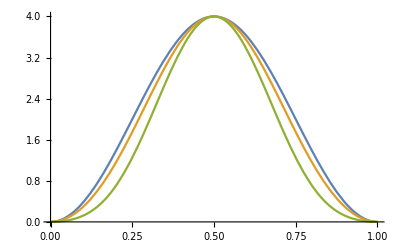

```mathematica
H0 = Plot[{4*1^2 Sin[1*Pi*x]^2,Q[Pi*x,Pi/6],Q[Pi*x,Pi/3]},{x,0,1}]
```

## Multiparameter-Theory

```mathematica
MatrixForm[Jx= (KroneckerProduct[sx,I2,I2]+KroneckerProduct[I2,sx,I2]+KroneckerProduct[I2,I2,sx])];
MatrixForm[Jy= (KroneckerProduct[sy,I2,I2]+KroneckerProduct[I2,sy,I2]+KroneckerProduct[I2,I2,sy])];
MatrixForm[Jz= (KroneckerProduct[sz,I2,I2]+KroneckerProduct[I2,sz,I2]+KroneckerProduct[I2,I2,sz])];
MatrixForm[ghz=1/(√2)(KroneckerProduct[u,u,u]+KroneckerProduct[d,d,d])];
```

```mathematica
(*{θx,θy,θz} = {π/10,π/10,π/10};*)
{θx,θy,θz} = {π/6,π/6,π/6};
(* change for other thetas *)
MatrixForm[Hami = FullSimplify[θx*Jx+θy*Jy+θz*Jz]];
MatrixForm[Evol3[t_] = FullSimplify[MatrixExp[-I*t*Hami]]];
MatrixForm[ghzt[t_] = FullSimplify[Evol3[t].ghz]];
```

```mathematica
(* Derivatives by integral *) 
MatrixForm[Ax[t_]  = ∫_0^t MatrixExp[-I*x*Hami].Jx.MatrixExp[I*x*Hami]ⅆx];
MatrixForm[Ay[t_]  = ∫_0^t MatrixExp[-I*x*Hami].Jy.MatrixExp[I*x*Hami]ⅆx];
MatrixForm[Az[t_]  = ∫_0^t MatrixExp[-I*x*Hami].Jz.MatrixExp[I*x*Hami]ⅆx];
```

```mathematica
(* QFIM *)
Qxx = 4*FullSimplify[ghz†.Ax[t].Ax[t].ghz - ghz†.Ax[t].ghz*ghz†.Ax[t].ghz, {t>0}];
Qxy = 4*FullSimplify[ghz†.Ax[t].Ay[t].ghz - ghz†.Ax[t].ghz*ghz†.Ay[t].ghz, {t>0}];
Qxz = 4*FullSimplify[ghz†.Ax[t].Az[t].ghz - ghz†.Ax[t].ghz*ghz†.Az[t].ghz, {t>0}];
Qyx = 4*FullSimplify[ghz†.Ay[t].Ax[t].ghz - ghz†.Ay[t].ghz*ghz†.Ax[t].ghz, {t>0}];
Qyy = 4*FullSimplify[ghz†.Ay[t].Ay[t].ghz - ghz†.Ay[t].ghz*ghz†.Ay[t].ghz, {t>0}];
Qyz = 4*FullSimplify[ghz†.Ay[t].Az[t].ghz - ghz†.Ay[t].ghz*ghz†.Az[t].ghz, {t>0}];
Qzx = 4*FullSimplify[ghz†.Az[t].Ax[t].ghz - ghz†.Az[t].ghz*ghz†.Ax[t].ghz, {t>0}];
Qzy = 4*FullSimplify[ghz†.Az[t].Ay[t].ghz - ghz†.Az[t].ghz*ghz†.Ay[t].ghz, {t>0}];
Qzz = 4*FullSimplify[ghz†.Az[t].Az[t].ghz - ghz†.Az[t].ghz*ghz†.Az[t].ghz, {t>0}];
MatrixForm[Qt[t_] = FullSimplify[{{Qxx[[1,1]],Qxy[[1,1]],Qxz[[1,1]]},{Qyx[[1,1]],Qyy[[1,1]],Qyz[[1,1]]},{Qzx[[1,1]],Qzy[[1,1]],Qzz[[1,1]]}}]];
```

((4 (66+π t (-12+5 π t)+12 (-6+π t) Cos[(π t)/(√3)]+6 Cos[(2 π t)/(√3)]-4 √3 (-3+π t) Sin[(π t)/(√3)]-6 √3 Sin[(2 π t)/(√3)]))/(3 π^2) | (4 (-42+5 π^2 t^2+54 Cos[(π t)/(√3)]-12 Cos[(2 π t)/(√3)]-4 √3 π t Sin[(π t)/(√3)]))/(3 π^2) | (4 (-24+π t (-6+5 π t)+6 (3+π t) Cos[(π t)/(√3)]+6 Cos[(2 π t)/(√3)]+2 √3 (-6+π t) Sin[(π t)/(√3)]+6 √3 Sin[(2 π t)/(√3)]))/(3 π^2)
(4 (-42+5 π^2 t^2+54 Cos[(π t)/(√3)]-12 Cos[(2 π t)/(√3)]-4 √3 π t Sin[(π t)/(√3)]))/(3 π^2) | (4 (66+π t (12+5 π t)-12 (6+π t) Cos[(π t)/(√3)]+6 Cos[(2 π t)/(√3)]-4 √3 (3+π t) Sin[(π t)/(√3)]+6 √3 Sin[(2 π t)/(√3)]))/(3 π^2) | (4 (-24+π t (6+5 π t)-6 (-3+π t) Cos[(π t)/(√3)]+6 Cos[(2 π t)/(√3)]+2 √3 (6+π t) Sin[(π t)/(√3)]-6 √3 Sin[(2 π t)/(√3)]))/(3 π^2)
(4 (-24+π t (-6+5 π t)+6 (3+π t) Cos[(π t)/(√3)]+6 Cos[(2 π t)/(√3)]+2 √3 (-6+π t) Sin[(π t)/(√3)]+6 √3 Sin[(2 π t)/(√3)]))/(3 π^2) | (4 (-24+π t (6+5 π t)-6 (-3+π t) Cos[(π t)/(√3)]+6 Cos[(2 π t)/(√3)]+2 √3 (6+π t) Sin[(π t)/(√3)]-6 √3 Sin[(2 π t)/(√3)]))/(3 π^2) | (4 (48+5 π^2 t^2-36 Cos[(π t)/(√3)]-12 Cos[(2 π t)/(√3)]+8 √3 π t Sin[(π t)/(√3)]))/(3 π^2))

```mathematica
MatrixForm[Qtinv[t_] = FullSimplify[Inverse[Qt[t]]]];
```

```mathematica
Sumtr[t_]=FullSimplify[Tr[ Qtinv[t]]]
```

(7 (6+π^2 t^2 Csc[(π t)/(2 √3)]^2))/(648 t^2)

```mathematica
7/216 (2/t^2+3 π^2 Csc[1/2 √3 π t]^2)
```

7/216 (2/t^2+3 π^2 Csc[1/2 √3 π t]^2)

```mathematica
7/(108 t^2)+(7 π^2 Csc[1/100 √3 π t]^2)/180000
```

7/(108 t^2)+(7 π^2 Csc[1/100 √3 π t]^2)/180000

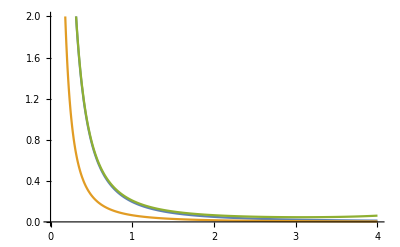

```mathematica
Plot[{Sumtr[t],7/(108 t^2),(7 (50/t^2+3 π^2 Csc[1/10 √3 π t]^2))/5400},{t,0,4}, PlotRange-> {0,2}]
```

```mathematica
N[Sumtr[t]]
```

```mathematica
N[-(1.5555555555555555*^-20 2.718281828459045^((0.+3.4641016151377545*^-10 ⅈ) t))/((-1.+2.718281828459045^((0.+3.4641016151377545*^-10 ⅈ) t))^2)]
```

-(1.55556×10^-20 2.71828^((0.+3.4641×10^-10 ⅈ) t))/((-1.+2.71828^((0.+3.4641×10^-10 ⅈ) t))^2)

```mathematica
Small:
```

```mathematica
-(7 ⅇ^((ⅈ √3 t)/5000000000))/(450000000000000000000 (-1+ⅇ^((ⅈ √3 t)/5000000000))^2)+7/(108 t^2)
```

```mathematica
(7*2)/216
```

7/108

```mathematica
7*6/648
```

7/108